# Monte Carlo methods:

## using monte Carlo to find the fraction of solutions that correspond to unstable nodes and saddle nodes of a linear system.

```mathematica
alist=Table[2(RandomReal[]-0.5),{i,1,10}]
```

{-0.828228,0.265778,-0.832582,0.270618,0.962471,0.944164,-0.505059,-0.788097,-0.88692,0.152551}

```mathematica
RandomReal[]
```

0.506346

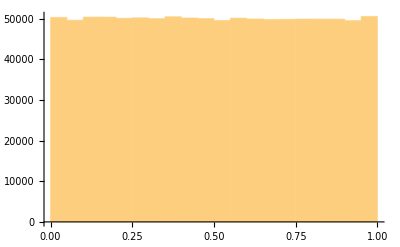

```mathematica
Histogram [Table[RandomReal[],{1000000}]]
```

```mathematica
data=Table[
alist=Table[2(RandomReal[]-0.5),{i,1,nmat}];
blist=Table[2(RandomReal[]-0.5),{i,1,nmat}];
clist=Table[2(RandomReal[]-0.5),{i,1,nmat}];
dlist=Table[2(RandomReal[]-0.5),{i,1,nmat}];
deltalist=alist*dlist-blist*clist;
taulist=alist+dlist;
disclist=taulist*taulist-4deltalist;
fracsaddle=Total[1-UnitStep[deltalist]]/Length[deltalist]//N;
fracunstablenode=Total[UnitStep[deltalist]UnitStep[taulist]UnitStep[disclist]]/Length[taulist]//N;
{nmat,fracsaddle,fracunstablenode},{nmat,100000,1000000,100000}];

ListLinePlot[data[[All,{1,3}]]]
```

-Graphics-

```mathematica
ListLinePlot[data[[All,{1,2}]]]
```

-Graphics-

## using Monte Carlo to estimate value of In(2) and pi , by integrating certain functions.

```mathematica
Integrate[1/(1+x),{x,0,1}]//N
```

0.693147

```mathematica
data=Table[n=2^k;
{n,Mean[Table[Mean[Table[1/(RandomReal[]+1),{n}]],{1000}]]},{k,5,10}];
```

```mathematica
TableForm[data]
```

32 | 0.694469
64 | 0.693195
128 | 0.6937
256 | 0.692787
512 | 0.693048
1024 | 0.693151

```mathematica
ListPlot[data,Joined->True]
```

-Graphics-

```mathematica
errdata=Table[n=2^k;
{n,Mean[Table[Abs[Mean[Table[1/(RandomReal[]+1),{n}]-Log[2]]],{1000}]]},{k,5,10}];
```

```mathematica
TableForm[errdata]
```

32 | 0.0198703
64 | 0.0138972
128 | 0.00958174
256 | 0.00678824
512 | 0.00480072
1024 | 0.00354658

```mathematica
ListPlot[errdata,Joined->True]
```

-Graphics-

```mathematica
fn[x_]=c * x^b;
fit=FindFit[errdata,{c x^b},{c,b},{x}]
```

{c→0.117275,b→-0.51292}

```mathematica
fn[x]/.fit;
```

```mathematica
Show[Plot[fn[x]/.fit,{x,0,1200}],ListPlot[errdata,Joined->True]]
```

-Graphics-

```mathematica
Show[%24,AxesStyle->Black]
```

-Graphics-

```mathematica
Integrate[4/((x)^2 +1),{x,0,1}]
```

π

```mathematica
data=Table[n=2^k;
{n,Mean[Table[Mean[Table[4/(RandomReal[]^2+1),{n}]],{1000}]]},{k,5,10}];
```

```mathematica
TableForm[data]
```

32 | 3.13952
64 | 3.14288
128 | 3.14258
256 | 3.14207
512 | 3.14363
1024 | 3.14181

```mathematica
ListPlot[data,Joined->True]
```

-Graphics-

```mathematica
errdata=Table[n=2^k;
{n,Mean[Table[Abs[Mean[Table[4/(RandomReal[]^2+1),{n}]-Log[2]]],{1000}]]},{k,5,10}];
```

```mathematica
TableForm[errdata]
```

32 | 2.45271
64 | 2.44323
128 | 2.4487
256 | 2.44692
512 | 2.44901
1024 | 2.44747

```mathematica
ListPlot[errdata,Joined->True]
```

-Graphics-

```mathematica
fn[x_]=c * x^b;
fit=FindFit[errdata,{c x^b},{c,b},{x}]
fn[x]/.fit;
Show[Plot[fn[x]/.fit,{x,0,1200}],ListPlot[errdata,Joined->True]]
```

{c→2.45029,b→-0.000179274}

-Graphics-